# Revolution Plot 3D - II

### Exemple 1

```mathematica
f[x_]:=2/(1+(x-2)^2)
```

```mathematica
a:=0
```

```mathematica
b:=4
```

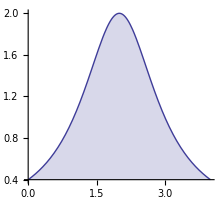

```mathematica
Plot[f[x],{x,a,b},AspectRatio->Automatic,Filling->Axis,PlotRange->All]
```

```mathematica
RevolutionPlot3D[f[x],{x,a,b},AxesLabel->{x,y,z},RevolutionAxis->"X"]
```

-Graphics3D-

Volume

```mathematica
∫_a^b π f[x]^2 ⅆx
```

4 π (2/5+ArcTan[2])

### Exemple 2

```mathematica
f1[x_]:=-1
```

```mathematica
f2[x_]:=Sin[x]-1
```

```mathematica
a:=0
```

```mathematica
b:=π
```

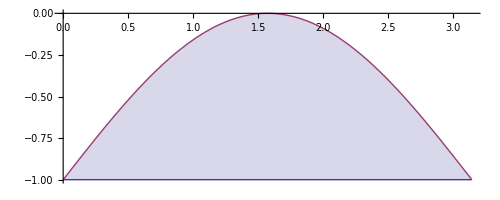

```mathematica
Plot[{f1[x],f2[x]},{x,a,b},AspectRatio->Automatic,Filling->{1->{2}}]
```

```mathematica
RevolutionPlot3D[{{x,f1[x]},{x,f2[x]}},{x,a,b},RevolutionAxis->"X"]
```

-Graphics3D-

Volume

```mathematica
∫_a^b (π f1[x]^2-π f2[x]^2)ⅆx
```

-1/2 (-8+π) π